## Первое приближение

```mathematica
ν0 = (3. 10^8)/(670 10^-9)/10^6; (* МГц *)
c = 3 10^8; (* м/c *)
Γ = 6 10^6 /10^6(* МГц *);
vQ = 1200; (* м/c *)
```

```mathematica
ClearAll[f1];
f1[s_, ν_] := f1[s, ν] = NIntegrate[
(1-s/(1 +s+ 4 (ν - ν0(1+ v/c))^2/Γ^2))
1/(1  + 4 (ν - ν0(1- v/c))^2/Γ^2)Exp[- v^2/vQ^2], {v, -2 vQ, + 2 vQ}, MaxRecursion->12];
```

```mathematica
f1[0, ν0]
```

6.30268

## Оценка сечения рассеяния

```mathematica
<<MaTeX`
```

```mathematica
kB= 1.38 10^-23;
ℏ = 1.054571817 10^-34;
Na = 6.02 10^23;
R = Na kB;
m = 0.007 / Na;
M = 0.007;
T = 300 + 273;
λ = 671 10^-9;

vQ = √((2 kB T)/m);
Print["тепловая скорость  <v> = ", ScientificForm[vQ, 2], " м/c"];

β = 1/6; 
κx = Log[1/β]/f1[0, ν0]; (* c/м *)
Print["феноменологическая оценка:       κ = ", ScientificForm[κx, 2]]
Print["феноменологическая оценка:  σ0 n l = ", ScientificForm[κx vQ √π, 2]]

ClearAll[GetP];
GetP[T_] := 133.32 10^(10.3454 -8345.57/T-8.84 10^-5 T - 0.68106 Log10[T]);
n = GetP[T]/(kB T);
Print["давление P = ", ScientificForm[GetP[T], 2], " Па"]
Print["концентрация n = ", ScientificForm[n, 2], " (:043c)^-3"]

σ0x = (3π)/8 λ^2;
Print["оценка рассеяния σ0x = ", ScientificForm[N@σ0x, 2], " (:043c)^2"]

lx = (κx vQ √π)/(n σ0x);
Print["оценка длины взаимодействия l = ", ScientificForm[100*lx, 2], " см"]
```

тепловая скорость  <v> = 1.2×10^3 м/c

феноменологическая оценка:       κ = 2.8×10^-1

феноменологическая оценка:  σ0 n l = 5.9×10^2

давление P = 9.5×10^-5 Па

концентрация n = 1.2×10^16 м^-3

оценка рассеяния σ0x = 5.3×10^-13 м^2

оценка длины взаимодействия l = 9.2 см

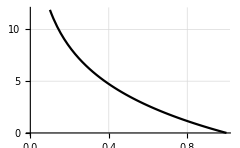

D:\Kami\git_folder\notes_5sem\rqc\saturation_spectr_simulation\lx.pdf

```mathematica
img = Plot[Log[1/β]/f1[0, ν0](vQ √π)/(n σ0x)100, {β, 0.1, 1}, PlotRange->{{0, 1}, Automatic}, GridLines->Automatic, AxesLabel->{MaTeX["\\beta = \\frac{I_{\\mathrm{out}}}{I_{\\mathrm{in}}}"], MaTeX["l,\ \\text{cm}"]}
, PlotStyle->Black, ImageSize->1.5{200, 100}]
Export[NotebookDirectory[]<>"lx.pdf", img]
```

```mathematica
lx = 0.1;
1/(vQ √π)n σ0x lx
```

0.298755